# Wilberforce Pendulum modelling PHYS1201 ASE project, 2022

## By Campbell McTernan and Aditya Singh Tejas

## Introduction

This project requires the creation and investigation of a complex mechanical system as least as complex as a double pendulum. For this task, we have chosen the Wilberforce pendulum which was first described by the physicist Lionel Robert Wilberforce  in 1896. The Wilberforce pendulum is constructed by hanging  a mass which is free to rotate in the direction of the coils, with certain harmonic properties which allow for energy to alternate between purely vertical and rotational motion. This is achieved through a coupling of the rotational and spring potential energy of the system. 

This investigation focuses on the description and analysis of the pendulum, using the Euler-Lagrange equations of motion to predict the pendulum’s path, and representing this in Mathematica. This document primarily serves to describe the theoretical implications of design choices for the pendulum and to predict its path using computational software.

## The Wilberforce Pendulum

The Wilberforce pendulum is made from a mass M connected to a spring of length l_1. The mass is a cylinder with an axis at a normal to the direction of the spring. It may be described by the vertical angle θ  and the rotational angle α, which is the angle the cylinder makes from its rest position. θ  is zero on the vertical, and α is zero when then cylinder axis is parallel with the x-y plane. Note that although technically the motion is technically in 3 dimensions, but the z-axis (into the page) is essentially irrelevant for motion equations, as it can be represented by α. 

The double pendulum is made of two masses, m_1 and m_2, and two rods of lengths l_1 and l_2. It may be described by two angles from the vertical, θ_1 and θ_2: see figure. These are zero on the vertical.


Note that since there are two coordinates, θ_1 and θ_2, there are two Euler-Lagrange equations. These must be solved simultaneously.

The mass m is free to slide along a frictionless rail. The Wilberforce pendulum consists of a cylindrical mass M (moment of inertia I) suspended by a helical spring of natural length l, spring constant k and torsional spring constant δ. The cylinder must hang such that its axis is always in the plane orthogonal to the direction of the spring, and is free to rotate along this plane. The spring makes an angle θ from the vertical and the tracked point on the cylinder creates an angle α from the measured from the starting point in its rotational plane . The horizontal position of the mass m is noted as x from the origin O : see figure. We choose the reference of the gravitational potential energy to be zero at the height of mass m. Note that the motion is actually in 3 dimensions but, the z-axis (into the page) is essential irrelevant for the motion of equations, as it can be represented by α.

### Deriving the Euler-Lagrange equations

Start by deriving the kinetic and potential energies, and hence the Lagrangian. Although you should formulate the dynamics using the angles, θ_1 and θ_2, it is easier to set it up in Cartesian coordinates:


We will start by considering all aspects of energy in the system to later conclude on the Lagrangian:

Kinetic energy
As the entire system is free to slide along a rail, the system can obtain velocity and thus kinetic energy. Defining  to be the velocity of the system, we thus have  . Furthermore, the cylinder  itself will have velocity relative to the system  and rotational energy dependant on the rotational velocity  given by  and  . 

Thus, the total kinetic energy of the system is  , so



Potential energy

We know that a spring with spring constant  and stretch length  has a spring potential  . We also know that the torsional potential of the spring is . Since these potentials are coupled, we furthermore have the potential  which represents the shared energy held during the transfer of energy between  and  in the system. As there are only two coupled components of potential, this relationship is linear and proportional to  and . Thus, assume  where  is some constant. Finally, as this Wilberforce experiment has been made unique by the inclusion of traditional swinging pendulum motion, we also have gravitational potential  . 

Thus, the total kinetic energy of the system is  , so



Lagrangian

αδϕθ

```mathematica
Subscript[x, 0] = x[t]; Subscript[y, 0] = 0;
Subscript[x, 1]=(l+s[t]) Sin[ θ[t]]+ Subscript[x, 0];Subscript[y, 1]=-(l+s[t]) Cos[θ[t]]+Subscript[y, 0];
Subscript[x, 2]=r Cos[α[t]] Cos[ θ[t]]+Subscript[x, 1];Subscript[y, 2]=r Cos[α[t]] Sin[ θ[t]]+Subscript[y, 1];
i = (1/12)M (2r)^2
```

```mathematica
(M r^2)/3
```

(M r^2)/3

The kinetic energy is then:

```mathematica
K=0.5 (m+M) (D[Subscript[x, 0],t]^2)+0.5 M(D[Subscript[x, 1],t]^2+D[Subscript[y, 1],t]^2)+0.5 i ((D[α[t], t])^2)
```

0.+0.166667 M r^2 α'[t]^2+0.5 M ((Sin[θ[t]] b'[t]+(l+b[t]) Cos[θ[t]] θ'[t])^2+(-Cos[θ[t]] b'[t]-(-l-b[t]) Sin[θ[t]] θ'[t])^2)

Use FullSimplify to simplify trigonometric terms.

```mathematica
K=FullSimplify[K]
```

```mathematica
0.5 M b'[t]^2+(0.5 m+0.5 M) x'[t]^2+0.16666666666666666 M r^2 α'[t]^2+M (0.5 l^2+1. l b[t]+0.5 b[t]^2) θ'[t]^2
```

0.5 M b'[t]^2+(0.5 m+0.5 M) x'[t]^2+0.166667 M r^2 α'[t]^2+M (0.5 l^2+1. l b[t]+0.5 b[t]^2) θ'[t]^2

Choose the potential energy zero to be at y_1 = y_2 = 0 :

```mathematica
V=0.5 k b[t]^2 + 0.5 δ α [ t ]^2 + ϕα [t] b[t]+ Mg Cos [θ[t]](l + b[t] )
```

0.5 k b[t]^2+Mg (l+b[t]) Cos[θ[t]]+0.5 δ α[t]^2+b[t] ϕα[t]

Use FullSimplify to simplify trigonometric terms.

```mathematica
V=FullSimplify[V]
```

0.5 k b[t]^2+Mg (l+b[t]) Cos[θ[t]]+0.5 δ α[t]^2+b[t] ϕα[t]

The Lagrangian :

```mathematica
L=K-V
```

0.-0.5 k b[t]^2-Mg (l+b[t]) Cos[θ[t]]-0.5 δ α[t]^2-b[t] ϕα[t]+0.166667 M r^2 α'[t]^2+0.5 M ((Sin[θ[t]] b'[t]+(l+b[t]) Cos[θ[t]] θ'[t])^2+(-Cos[θ[t]] b'[t]-(-l-b[t]) Sin[θ[t]] θ'[t])^2)

Next calculate the derivatives in the Euler-Lagrange equation:

```mathematica
dLdθ=D[L,θ[t]] (* θ derivative *)
```

Mg (l+b[t]) Sin[θ[t]]

```mathematica
dLdα=D[L,α[t]] (* α derivative *)
```

-ϕ b[t]-1. 𝛿 α[t]

```mathematica
dLdashdθ=D[L,θ'[t]] (* θ' derivative *)
```

2 M (0.5 l^2+1. l b[t]+0.5 b[t]^2) θ'[t]

```mathematica
dLdashα=D[L,α'[t]] (* α' derivative *)
```

1. Cos[θ_1[t]-θ_2[t]] l_1 l_2 m_2 θ_1'[t]+1. l_2^2 m_2 θ_2'[t]

```mathematica
dLdx=D[L,x[t]] (* α derivative *)
```

0

```mathematica
dLdashdx=D[L,x'[t]] (* x' derivative *)
```

0

Calculate the Euler-Lagrange equation for θ:

```mathematica
ELEθ= 0==FullSimplify[dLdθ-D[dLdashdθ,t]]
```

0==l_1 (m_1 (-1. g Sin[θ_1[t]]-1. l_1 θ_1''[t])+m_2 (-1. g Sin[θ_1[t]]-1. l_1 θ_1''[t]+l_2 (-1. Sin[θ_1[t]-θ_2[t]] θ_2'[t]^2-1. Cos[θ_1[t]-θ_2[t]] θ_2''[t])))

Calculate the Euler-Lagrange equation for α:

```mathematica
ELEα= 0==FullSimplify[dLdα-D[dLdashdα,t]]
```

0==l_2 m_2 (-1. g Sin[θ_2[t]]+l_1 (1. Sin[θ_1[t]-θ_2[t]] θ_1'[t]^2-1. Cos[θ_1[t]-θ_2[t]] θ_1''[t])-1. l_2 θ_2''[t])

### Numerically solving the Euler-Lagrange equations

Choose the parameters.

```mathematica
m=0.002;M=0.3; g=9.8;l=0.3;r=0.05; ϕ = 0.3;
```

Solve the Euler-Lagrange equations:

```mathematica
solndp=NDSolve[{Subscript[ELEθ, 1],Subscript[ELEθ, 2],Subscript[θ, 1][0]==0,Subscript[θ, 2][0]==Pi/2,Subscript[θ, 1]'[0]==0,Subscript[θ, 2]'[0]==0},{Subscript[θ, 1],Subscript[θ, 2]},{t,0,10}]
```

{{θ_1→InterpolatingFunction[…],θ_2→InterpolatingFunction[…]}}

Plot y_1 and y_2 coordinates vs time. Include a title for the plot and axes labels with units.

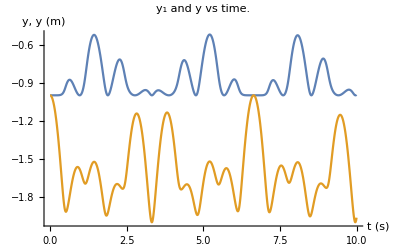

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y (m)"},PlotLabel->"y_1 and y vs time."]
```

Plot trajectories in x, y plane.

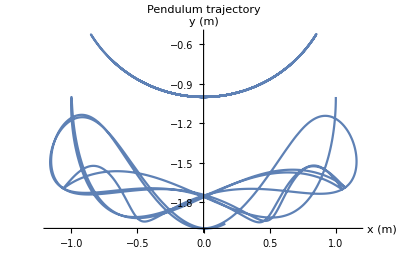

```mathematica
ParametricPlot[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp,{t,0,10},PlotRange->All,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory"]
```

Animate trajectories in x, y plane.

```mathematica
Animate[ParametricPlot[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]}}/.solndp,{t,0,tend},PlotRange->{{-1.5,1.5},{-2.5,0}},AxesLabel->{"x (m)","y (m)"},PlotLabel->"Pendulum trajectory"],{tend,0,10},AnimationRepetitions->3]
```

### Adding damping

We add terms proportional to the angular velocities θ_1' and θ_2' with the same proportionality constant α.

Damped dynamical equations:

```mathematica
ELEθoneDamped=0==FullSimplify[D[Subscript[dLdashdθ, 1],t]-Subscript[dLdθ, 1] +α Subscript[θ, 1]'[t]]
```

0==19.6 Sin[θ_1[t]]+1. α θ_1'[t]+1. Sin[θ_1[t]-θ_2[t]] θ_2'[t]^2+2. θ_1''[t]+1. Cos[θ_1[t]-θ_2[t]] θ_2''[t]

```mathematica
ELEθtwoDamped=0==FullSimplify[D[Subscript[dLdashdθ, 2],t]-Subscript[dLdθ, 2] +α Subscript[θ, 2]'[t]]
```

0==9.8 Sin[θ_2[t]]-1. Sin[θ_1[t]-θ_2[t]] θ_1'[t]^2+1. α θ_2'[t]+1. Cos[θ_1[t]-θ_2[t]] θ_1''[t]+1. θ_2''[t]

Choose the damping parameter and solve the Euler-Lagrange equation:

```mathematica
α=0.01; soln=NDSolve[{ELEθoneDamped,ELEθtwoDamped, Subscript[θ, 1][0]==0,Subscript[θ, 2][0]==Pi/2,Subscript[θ, 1]'[0]==0,Subscript[θ, 2]'[0]==0},{Subscript[θ, 1],Subscript[θ, 2]},{t,0,10}]
```

{{θ_1→InterpolatingFunction[{{0., 10.}}, <>],θ_2→InterpolatingFunction[{{0., 10.}}, <>]}}

Plot y_1 and y_2 coordinates vs time. Include a title for the plot and axes labels with units.

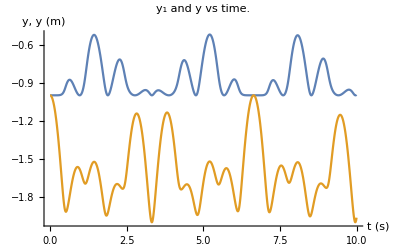

```mathematica
Plot[Evaluate[{Subscript[y, 1],Subscript[y, 2]}/.solndp],{t,0,10},PlotRange->All,AxesLabel->{"t (s)","y, y (m)"},PlotLabel->"y_1 and y vs time."]
```